## Restricted Three-Body Problem

```mathematica
solution[orbtime_,VZi_,VRi_,μ1_,μ2_,Zi_,Ri_,Jz_,a_]:=NDSolve[{E3[t]== 
Z[t]/a(-mm[t]/rm[t]+mp[t]/rp[t]) +(Z[t]^2/a^2)Jz^2/(2 R[t]^2)+1/2 Z'[t]^2+1/2 ((Z[t] R'[t])/a-(R[t] Z'[t])/a)^2,
E0[t]== -mm[t]/rm[t]-mp[t]/rp[t]+Jz^2/(2 R[t]^2)+1/2 R'[t]^2+1/2 Z'[t]^2,
Φ[t]==-mm[t]/rm[t]-mp[t]/rp[t],
Pt'[t]==Φ[t],
WZt'[t]==Z[t](-Z''[t]),
WRt'[t]==R[t](-R''[t]),
KZt'[t]==Z'[t]^2,
KRt'[t]== R'[t]^2,
rp[t]==√((Z[t]+a)^2+R[t]^2),rm[t]==√((Z[t]-a)^2+R[t]^2),
mp[t]==μ1 ,
mm[t]==μ2 ,
Z''[t]==-((Z[t]+a)*(mp[t]))/rp[t]^3-((Z[t]-a)*(mm[t]))/rm[t]^3,R''[t]==-((R[t])*(mp[t]))/rp[t]^3-((R[t])*(mm[t]))/rm[t]^3+Jz^2/R[t]^3,θ'[t]==Jz/R[t]^2,θ[0]==0,WZt[0]==0,WRt[0]==0,KZt[0]==0,KRt[0]==0,Pt[0]==0,Z[0]==Zi,R[0]==Ri,Z'[0]==VZi,R'[0]==VRi},{θ,Z,R,E3,E0,Φ,Pt,WZt,WRt,KZt,KRt},{t,0,orbtime},PrecisionGoal->6,Method->Automatic ]
```

## DETAILS

The equations of motion are

Z''(t)==2 R'(t)+Z(t)-(μ_1 (μ_2+Z(t)))/(((μ_2+Z(t))^2+(R(t))^2)^(3/2))-(μ_2 (Z(t)-μ_1))/(((Z(t)-μ_1)^2+(R(t))^2)^(3/2));

R''(t)==R(t)-2 Z'(t)-(μ_1 R(t))/(((μ_2+Z(t))^2+(R(t))^2)^(3/2))-(μ_2 R(t))/(((Z(t)-μ_1)^2+(R(t))^2)^(3/2)),

where μ_i are the reduced masses, while Z and R are the coordinates in the rotating sRstem. The small bodR is subjected to both centrifugal and Coriolis forces.

In some cases, the third mass appears to orbit around points other than the large masses. These are called "Lagrange points"; there are five such equilibrium states in the co-rotating sRstem.

THIS NOTEBOOK IS THE SOURCE CODE FROM

Enrique ZelenR

"Restricted Three-BodR Problem in a Plane"
 http://demonstrations.wolfram.com/RestrictedThreeBodRProblemInAPlane/
 Wolfram Demonstrations Project
 Published: October 29, 2012

A full-function Wolfram Mathematica system is required to edit this notebook.
GET WOLFRAM MATHEMATICA »

© Wolfram Demonstrations Project & Contributors   |   Terms of Use   |   Make a new version of this Demonstration »

```mathematica
"Plot of postion in cartesian cooridnates, to visualise the orbit. Parameters of solution be changed manually, they are: (orbtime_,VZi_,VRi_,μ1_,μ2_,Zi_,Ri_,Jz_,a_)"
"orbtime is time the simulation is run for, VZi and VRi are intital velocities in Z and R, μ1 and μ2 are black hole masses, Ri and Zi are intial positions in R and Z, Jz in angular momentum in Z, a is the distance of the black holes from the origin, so 2a is black hole seperation"
```

```mathematica
Show[ParametricPlot3D[Evaluate[{R[t]*Cos[θ[t]],R[t]*Sin[θ[t]],Z[t]}/.solution[0.5, 2, 2, 8,8, 0.1,  0.1,1,0.1]],{t,0,0.5}],Graphics3D[{Red, PointSize[0.01], Point[{0,0.1,0}],
     Point[{0,-0.1,0}]}]]
```

-Graphics3D-

```mathematica
"test of energy conservation"
```

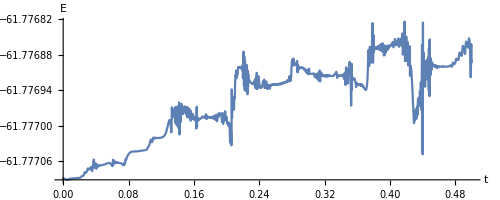

```mathematica
Plot[Evaluate[E0[t]/.solution[0.5, 2, 2, 8,8, 0.1,  0.1,1,0.1]],{t,0,0.5},AspectRatio->Full, AxesLabel->{"t","E"}]
```

```mathematica
"Defining equations for calculating angular momentum and distance relative to each black hole"
```

```mathematica
J1 = Sqrt[(-(Z[t]+0.1)*R[t]*θ'[t])^2+((R[t]*Z'[t])+(-(Z[t]+0.1)*R'[t]))^2+(R[t]*R[t]*θ'[t])^2]
J2 =  Sqrt[(-(Z[t]-0.1)*R[t]*θ'[t])^2+((R[t]*Z'[t])+(-(Z[t]-0.1)*R'[t]))^2+(R[t]*R[t]*θ'[t])^2]
R1 = Sqrt[((Z[t]+0.1)^2+R[t]^2)]
R2 = Sqrt[((Z[t]-0.1)^2+R[t]^2)]
```

√(((-0.1-Z[t]) R'[t]+R[t] Z'[t])^2+R[t]^4 θ'[t]^2+R[t]^2 (-0.1-Z[t])^2 θ'[t]^2)

√(((0.1-Z[t]) R'[t]+R[t] Z'[t])^2+R[t]^4 θ'[t]^2+R[t]^2 (0.1-Z[t])^2 θ'[t]^2)

√(R[t]^2+(0.1+Z[t])^2)

√(R[t]^2+(-0.1+Z[t])^2)

```mathematica
"Plot of Angular momentum relative to one black hole vs. relative to the other"
```

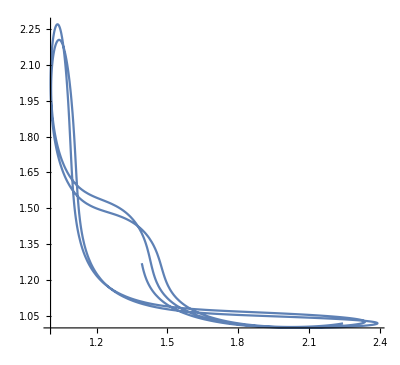

```mathematica
ParametricPlot[Evaluate[{J1,J2}/.solution[0.5, 2, 2, 8,8, 0.1,  0.1,1,0.1]],{t,0,0.5},AspectRatio->Full]
```

```mathematica
"plot of ditance to one blakc hole vs. distance to the other"
```

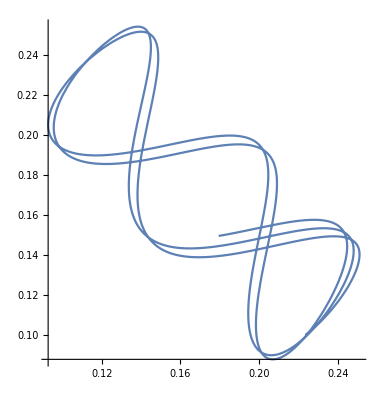

```mathematica
ParametricPlot[Evaluate[{R1,R2}/.solution[0.5, 2, 2, 8,8, 0.1,  0.1,1,0.1]],{t,0,0.5},AspectRatio->Full]
```

```mathematica
"defining inital velocity to launch star with, and introducing a method to vary the angle of launch"
```

```mathematica
Vesc = Sqrt[(2*8)/0.1]

k =1
α = k*π/18
```

12.6491

1

π/18

```mathematica
"plot of position in R vs. position in Z"
```

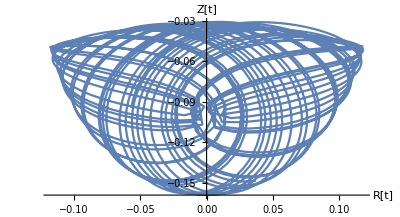

```mathematica
Show[ParametricPlot[Evaluate[{R[t],Z[t]}/.solution[10,Vesc*Cos[α],Vesc*Sin[α],8,8,-0.1+0.02*Cos[α],0.02*Sin[α],0,0.1]],{t,0,1.5},AxesLabel->{"R[t]","Z[t]"}],Graphics[{Red,PointSize[0.01],Point[{0.1,0}],Point[{-0.1,0}]}]]
```

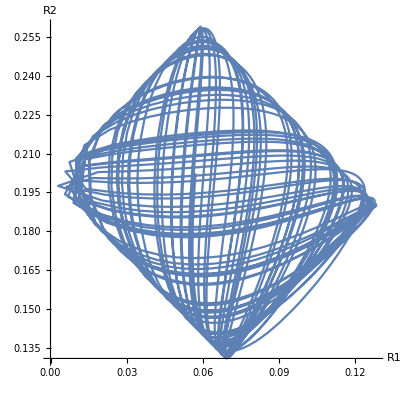

```mathematica
ParametricPlot[Evaluate[{R1,R2}/.solution[10,Vesc*Cos[α],Vesc*Sin[α],8,8,-0.1+0.02*Cos[α],0.02*Sin[α],0,0.1]],{t,0,1.5},AxesLabel->{"R1","R2"},AspectRatio->Full]
```